```mathematica
zs = 3;
zbk = 2;
```

```mathematica
normalConst = Integrate[(x+lbk)^zs*Exp[-x],{x,0,Infinity}];
```

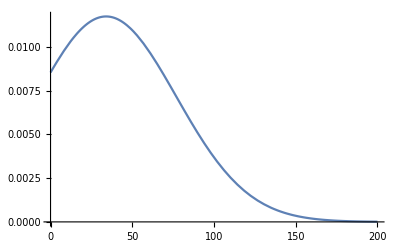

```mathematica
Plot[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,200}]
```

```mathematica
Integrate[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,Infinity}]
```

1

```mathematica
probDist=ProbabilityDistribution[(x+lbk)^zs*Exp[-x]/normalConst,{x,0,Infinity}];
```

```mathematica
mu=N[Mean[probDist]]
sig=N[StandardDeviation[probDist]]
```

50.4055

32.8158746465492

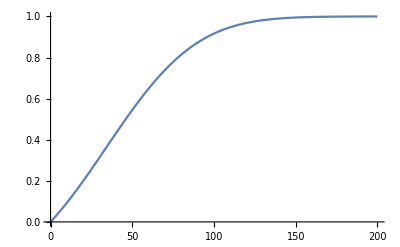

```mathematica
Plot[CDF[probDist,x],{x,0,200}]
```

```mathematica
Plot[PDF[probDist,x],{x,0,200}]
```

-Graphics-

we want it to be larger than 99,7%

```mathematica
1-N[Probability[x>mu+3.3*sig,x\[Distributed]probDist]]
```

0.997068

```mathematica
NSolve[N[CDF[probDist,a]]==0.99,a]
```

NSolve[(Piecewise[{{5.01743550102×10^-5201 (1.9930500348×10^5200-1. Gamma[1838.,1803.+a]), a>0.}, {0., True}}])==0.99,a]

```mathematica
mu+3.3*sig
```

158.698

```mathematica
NSolve[N[Probability[x>a,x\[Distributed]probDist]]==0.01,a]
```

NSolve[(Piecewise[{{1., a≤0.}, {-1.20504×10^-12+5.01743550102×10^-5201 Gamma[1838.,1803.+a], True}}])==0.01,a]

```mathematica
lbkDist = PDF[GammaDistribution[zbk+1,1],x];
```

Piecewise[{{1/6 ⅇ^-x x^3, x>0}, {0, True}}]

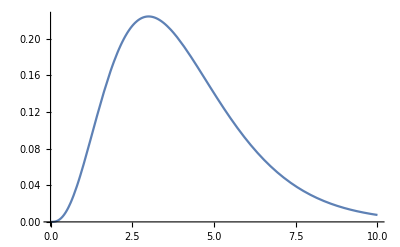

```mathematica
Plot[lbkDist,{x,0,10}]
```

```mathematica
finalDist=TransformedDistribution[(x+lbk)^zs*Exp[-x],lbk\[Distributed]GammaDistribution[zbk+1,1]]
```

TransformedDistribution[ⅇ^-x (x+x)^3,x\[Distributed]GammaDistribution[3,1]]

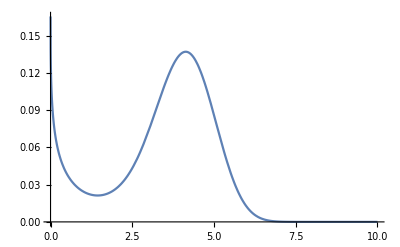

```mathematica
Plot[PDF[finalDist,x],{x,0,10}]
```

```mathematica
finalDist=TransformedDistribution[probDist,lbk\[Distributed]GammaDistribution[zbk+1,1]]
```

```mathematica
zs
```

3